# Метод на хордите

Задача: Дадено е уравенението:
x^5 + 103 sin x  - 34 x^3 - 23 = 0
1. Да се визуализира функцията и да се определят броя на корените.
2. Да се локализира един от корените.
3. Уточнете локализирания корен по метода на хордите.
	- проверка на сходимост
	- избор на начално приближение и постоянна точка
	- итерациите
4. Оценка на грешката.
5. Колко биха били броя на итерациите за достигане на точност 0.0001 по метода на разполовяването, използвайки интервала от локализацията на корена. Направете сравнение между двата метода.

```mathematica
f[x_]:=  x^5+103 Sin[x]-34 x^3-23
```

```mathematica
f[x]
```

-23-34 x^3+x^5+103 Sin[x]

## 1. Да се визуализира функцията и да се определят броя на корените.

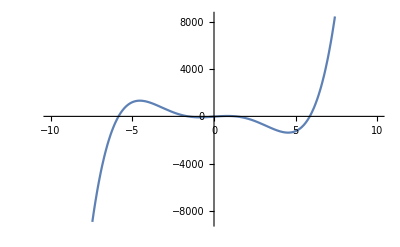

```mathematica
Plot[f[x],{x,-10,10}]
```

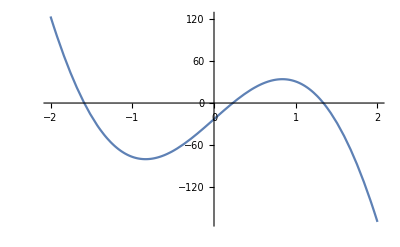

```mathematica
Plot[f[x],{x,-2,2}]
```

## 2. Да се локализира един от корените.

Локализираме най-малкия корен

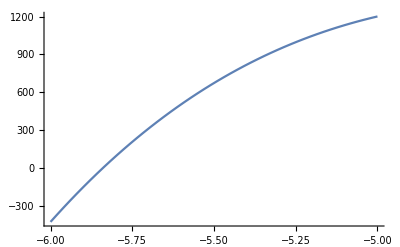

```mathematica
Plot[f[x],{x,-6,-5}]
```

```mathematica
f[-6.]
```

-426.22

```mathematica
f[-5.]
```

1200.77

Извод:
(1) Функцията е непрекъсната, защото е сума от непрекъснати функции (полином и синус)
(2) f(-6) = -426.22... < 0
       f(-5) = 1200.77... > 0
       => Функцията има различни знаци в двата края на разглеждания интервал [-6; -5].
       От (1) и (2) следва, че функцията има поне един корен в разглеждания интервал [-6; -5].

## 3. Уточнете локализирания корен по метода на хордите.

### Проверка на сходимост

#### Графика на първата производна

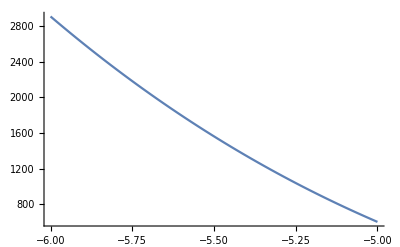

```mathematica
Plot[f'[x],{x,-6,-5}]
```

Извод: (1) Стойностите на първата производна в разглеждания интервал [-6; -5] са между 500 и 3000. Следователно първата f’(x) > 0 в целия разглеждан интервал [-6; -5].

#### Графика на втората производна

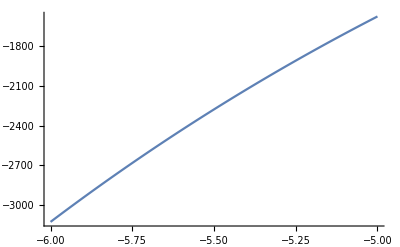

```mathematica
Plot[f''[x],{x,-6,-5}]
```

Извод: (2) Стойностите на втората производна в разглеждания интервал [-6; -5] са между -3500 и -1500. Следователно втората f’’ (x) < 0 в целия разглеждан интервал [-6; -5] .

Извод: От (1) и (2) следва, че първата и втората производна имат еднакви знаци в разглеждания интервал [-6; -5]. Следователно условията за сходимост на метода на хордите са изпълнени.

### Избор на начално приближение и постоянна точка

Пояснение как е избрано..... (формулата от файла или друго)

```mathematica
p = -6.
x0 = -5.
```

-6.

-5.

### Итерациите

```mathematica
For[n = 0, n <= 3, n++,
x1 = x0 - f[x0]/(f[x0] - f[p])*(x0 - p);
Print["n = ",n,  " x_n = ", x1];
x0 = x1
]
```

n = 0 x_n = -5.73803

n = 1 x_n = -5.83075

n = 2 x_n = -5.83923

n = 3 x_n = -5.83998

```mathematica
x0 = -5.
```

-5.

```mathematica
For[n = 0, n <= 10, n++,
x1 = x0 - f[x0]/(f[x0] - f[p])*(x0 - p);
Print["n = ",n,  " x_n = ", x1];
x0 = x1
]
```

n = 0 x_n = -5.73803

n = 1 x_n = -5.83075

n = 2 x_n = -5.83923

n = 3 x_n = -5.83998

n = 4 x_n = -5.84005

n = 5 x_n = -5.84006

n = 6 x_n = -5.84006

n = 7 x_n = -5.84006

n = 8 x_n = -5.84006

n = 9 x_n = -5.84006

n = 10 x_n = -5.84006

```mathematica
f[x_]:=  x^5+103 Sin[x]-34 x^3-23
x0 = -5.; p = -6;
For[n = 0, n <= 10, n++,
x1 = x0 - f[x0]/(f[x0] - f[p])*(x0 - p);
Print["n = ",n,  " x_n = ", x1];
x0 = x1
]
```

## 4. Оценка на грешката

### Изчисляване на постоянните величини

```mathematica
Plot[Abs[f'[x]],{x,-6,-5}]
```

-Graphics-

От геометрично съображение максимума на абсолютната стойност на първата производна се достига в левия край на интервала, а минимума - в десния.

```mathematica
M1 = Abs[f'[-6.]]
```

2906.9

```mathematica
m1 = Abs[f'[-5.]]
```

604.217

```mathematica
R = (M1 - m1)/m1
```

3.81101

```mathematica
f[x_]:=  x^5+103 Sin[x]-34 x^3-23
x0 = -5.; p = -6;
M1 = Abs[f'[-6.]];
m1 = Abs[f'[-5.]];
R = (M1 - m1)/m1;
For[n = 0, n <= 10, n++,
x1 = x0 - f[x0]/(f[x0] - f[p])*(x0 - p);
Print["n = ",n,  " x_n = ", x1, " f(x_n) = ", f[x1], " ε_n = ", eps = R * Abs[x1 - x0]];
x0 = x1
]
```

n = 0 x_n = -5.73803 f(x_n) = 233.504 ε_n = 2.81265

n = 1 x_n = -5.83075 f(x_n) = 22.4867 ε_n = 0.353364

n = 2 x_n = -5.83923 f(x_n) = 1.9943 ε_n = 0.0323239

n = 3 x_n = -5.83998 f(x_n) = 0.175555 ε_n = 0.0028534

n = 4 x_n = -5.84005 f(x_n) = 0.0154435 ε_n = 0.000251076

n = 5 x_n = -5.84006 f(x_n) = 0.00135849 ε_n = 0.0000220863

n = 6 x_n = -5.84006 f(x_n) = 0.000119499 ε_n = 1.94282×10^-6

n = 7 x_n = -5.84006 f(x_n) = 0.0000105116 ε_n = 1.70899×10^-7

n = 8 x_n = -5.84006 f(x_n) = 9.24651×10^-7 ε_n = 1.5033×10^-8

n = 9 x_n = -5.84006 f(x_n) = 8.13361×10^-8 ε_n = 1.32237×10^-9

n = 10 x_n = -5.84006 f(x_n) = 7.15681×10^-9 ε_n = 1.16321×10^-10

Цикъл със стоп-критерий при определена точност

```mathematica
f[x_]:=  x^5+103 Sin[x]-34 x^3-23
x0 = -5.; p = -6;
M1 = Abs[f'[-6.]];
m1 = Abs[f'[-5.]];
R = (M1 - m1)/m1;
epszad = 0.0001;
eps = 1;
Print["n = ",0,  " x_n = ", x0, " f(x_n) = ", f[x0]];
For[n = 1, eps > epszad, n++,
x1 = x0 - f[x0]/(f[x0] - f[p])*(x0 - p);
Print["n = ",n,  " x_n = ", x1, " f(x_n) = ", f[x1], " ε_n = ", eps = R * Abs[x1 - x0]];
x0 = x1
]
```

n = 0 x_n = -5. f(x_n) = 1200.77

n = 1 x_n = -5.73803 f(x_n) = 233.504 ε_n = 2.81265

n = 2 x_n = -5.83075 f(x_n) = 22.4867 ε_n = 0.353364

n = 3 x_n = -5.83923 f(x_n) = 1.9943 ε_n = 0.0323239

n = 4 x_n = -5.83998 f(x_n) = 0.175555 ε_n = 0.0028534

n = 5 x_n = -5.84005 f(x_n) = 0.0154435 ε_n = 0.000251076

n = 6 x_n = -5.84006 f(x_n) = 0.00135849 ε_n = 0.0000220863

## Сравнение между методите

Колко биха били броя на итерациите за достигане на точност 0.0001 по метода на разполовяването, използвайки интервала от локализацията на корена . Направете сравнение между двата метода .

```mathematica
Log2[(-5 - (-6))/0.0001] - 1
```

12.2877

Извод: По метода на разполовяването биха били необходими 13 итерации за достигане на исканата точност. А по метода на хордите бяха достатъчни 5 итерации. Следователно методът на хордите е по-ефективен.